```mathematica
SetDirectory[NotebookDirectory[]];
```

## Growth factor

```mathematica
outputs=Import["../data/growth_factor_unimodal_outputs.csv"];
```

```mathematica
fSplit[vData__,aLen_Integer]:=Table[vData[[(1 + (i-1) aLen);;i aLen,All]],{i,1,(Length@vData)/aLen,1}]
fPostWarmup[splitData__]:=Block[{aLen=Length@splitData[[1]]},Table[splitData[[i]][[aLen/2;;]],{i,1,Length@splitData,1}]]
```

```mathematica
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]],100];
dist2=SmoothKernelDistribution[test[[All,2]],100];
```

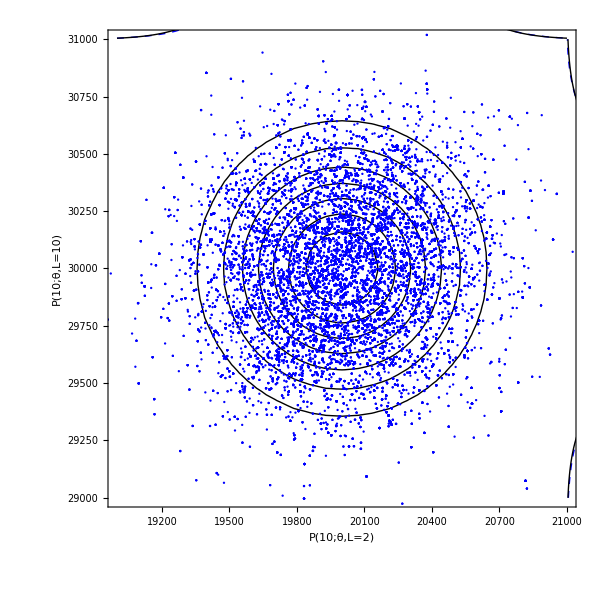
-Graphics-A.

```mathematica
gUniform=Labeled[Show[ContourPlot[PDF[MultinormalDistribution[{2 10^4,3 10^4},10^5 IdentityMatrix[2]],{x,y}],{x,19000,21000},{y,29000,31000},ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{120,120},{40,120}},Frame->True,FrameLabel->{"P(10;θ,L=2)","P(10;θ,L=10)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,Epilog->{{Blue,Dashed,Line[Table[{x,31000+500000 PDF[dist1,x]},{x,19000,21000,20}]]},{Black,Line[Table[{x,31000+500000PDF[NormalDistribution[2 10^4, Sqrt[10^5]],x]},{x,19000,21000,20}]]},{{Dashed,Blue,Line[Table[{21000+500000PDF[dist2,x],x},{x,29000,31000,20}]]},{Black,Line[Table[{21000+500000PDF[NormalDistribution[3 10^4,Sqrt[10^5]],x],x},{x,29000,31000,20}]]}}}],ListPlot[test,PlotRange->{{19000,21000},{29000,31000}},PlotStyle->Blue],ImageSize->600],"A.",{{Top,Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
inputs=Import["../data/growth_factor_unimodal_inputs.csv"];
```

```mathematica
test1=fSplit[inputs,10000];
test1 = Flatten[fPostWarmup[test1],1];
```

```mathematica
mBounds={{2.5 10^5,8 10^5},{0.1,0.5},{0.25,3.0},{2,20},{0.005,0.03}};
```

```mathematica
Subscript[k,deg]
```

k_deg

```mathematica
parameters={"R_T","k_deg*","k_1","k_-1","k_deg"};
```

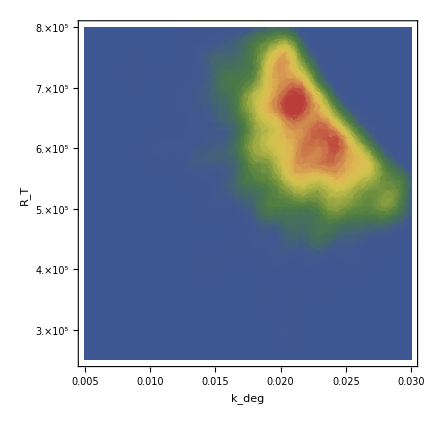
-Graphics-B.

```mathematica
i=5;
j=1;
gUniformInput2=Labeled[SmoothDensityHistogram[test1[[All,{i,j}]],Mesh->20,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{mBounds[[i,1]],mBounds[[i,2]]},{mBounds[[j,1]],mBounds[[j,2]]}},FrameLabel->{parameters[[i]],parameters[[j]]},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->435,Frame->{True,True,False,False},FrameTicks->{Automatic,{#,ScientificForm@#}&/@Table[300000.+100000 i,{i,0,5,1}]}],"B.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

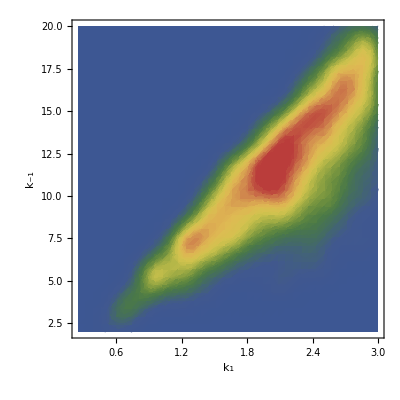
-Graphics-A.

```mathematica
gUniformInput1=Labeled[SmoothDensityHistogram[test1[[All,{3,4}]],Mesh->20,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.25,3},{2,20}},Frame->{True,True,False,False},FrameLabel->{"k_1","k_-1"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400],"A.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
summary1=Transpose@{Quantile[#,0.025],Quantile[#,0.25],Median[#],Quantile[#,0.75],Quantile[#,0.975]}&@test1;
summary1=Round[summary1,0.001];
```

```mathematica
Grid@summary1
```

441006. | 548275. | 606439. | 677055. | 772484.
0.197 | 0.335 | 0.396 | 0.444 | 0.492
0.895 | 1.688 | 2.165 | 2.562 | 2.95
4.349 | 8.351 | 11.235 | 14.226 | 18.709
0.013 | 0.019 | 0.021 | 0.024 | 0.029

```mathematica
(summary1[[All,4]]-summary1[[All,2]])/(mBounds[[All,2]]-mBounds[[All,1]])
```

{0.234144,0.2725,0.317818,0.326389,0.2}

## Growth factor (non-uniform)

```mathematica
inputs=Import["../data/growth_factor_nonuniform_inputs.csv"];
```

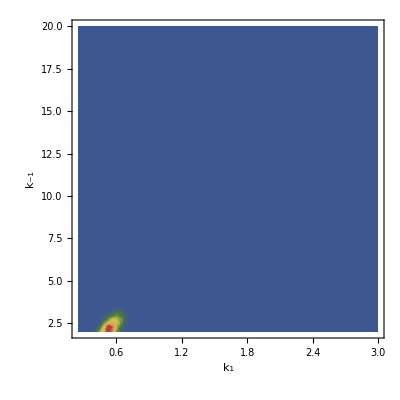
-Graphics-C.

```mathematica
test2=fSplit[inputs,10000];
test2 = Flatten[fPostWarmup[test2],1];
gNonuniformInput1=Labeled[SmoothDensityHistogram[test2[[All,{3,4}]],Mesh->10,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.25,3},{2,20}},Frame->{True,True,False,False},FrameLabel->{"k_1","k_-1"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400],"C.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
Subscript[R,T]
```

R_T

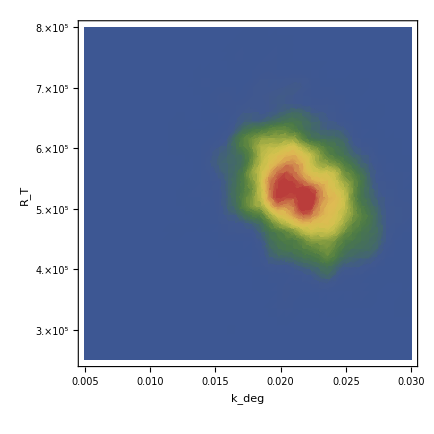
-Graphics-D.

```mathematica
i=5;
j=1;
gNonUniformInput2=Labeled[SmoothDensityHistogram[test2[[All,{i,j}]],Mesh->20,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{mBounds[[i,1]],mBounds[[i,2]]},{mBounds[[j,1]],mBounds[[j,2]]}},FrameLabel->{parameters[[i]],parameters[[j]]},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->435,Frame->{True,True,False,False},FrameTicks->{Automatic,{#,ScientificForm@#}&/@Table[300000.+100000 i,{i,0,5,1}]},ImagePadding->Automatic],"D.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
outputs=Import["../data/growth_factor_nonuniform_outputs.csv"];
```

```mathematica
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]],100];
dist2=SmoothKernelDistribution[test[[All,2]],100];
```

```mathematica
SmoothKernelDistribution
```

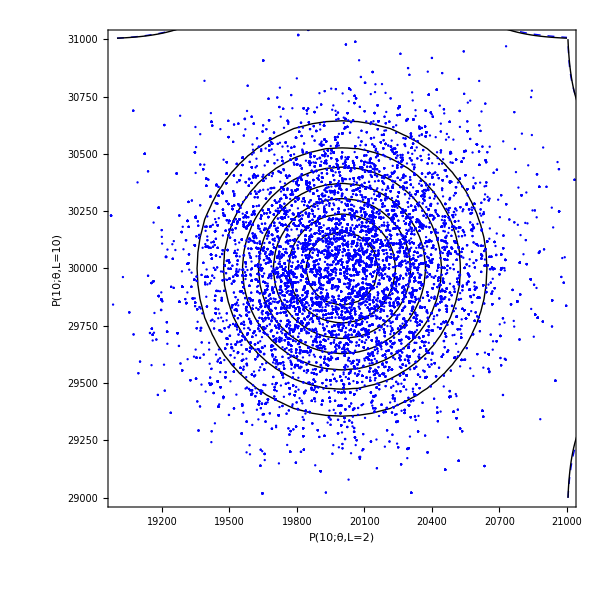
-Graphics-B.

```mathematica
gNonuniform=Labeled[Show[ContourPlot[PDF[MultinormalDistribution[{2 10^4,3 10^4},10^5 IdentityMatrix[2]],{x,y}],{x,19000,21000},{y,29000,31000},PlotRange->{{19000,21000},{29000,31000}},ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{120,120},{40,120}},Frame->True,FrameLabel->{"P(10;θ,L=2)","P(10;θ,L=10)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,Epilog->{{Blue,Dashed,Line[Table[{x,31000+500000 PDF[dist1,x]},{x,19000,21000,20}]]},{Black,Line[Table[{x,31000+500000PDF[NormalDistribution[2 10^4, Sqrt[10^5]],x]},{x,19000,21000,20}]]},{{Blue,Dashed,Line[Table[{21000+500000PDF[dist2,x],x},{x,29000,31000,20}]]},{Black,Line[Table[{21000+500000PDF[NormalDistribution[3 10^4,Sqrt[10^5]],x],x},{x,29000,31000,20}]]}}}],ListPlot[test,PlotRange->{{19000,21000},{29000,31000}},PlotStyle->Blue],ImageSize->600],"B.",{{Top,Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
gOutput=GraphicsRow[{gUniform,gNonuniform},ImageSize->1300]
```

-Graphics-

```mathematica
Export["../figures/growth_factor_outputs.pdf",gOutput]
```

../figures/growth_factor_outputs.pdf

```mathematica
gInput=Grid[{{gUniformInput1,gUniformInput2},{gNonuniformInput1,gNonUniformInput2}}]
```

-Graphics-A. | -Graphics-B.
-Graphics-C. | -Graphics-D.

```mathematica
Export["../figures/growth_factor_inputs.png",gInput,ImageResolution->500]
```

../figures/growth_factor_inputs.png

```mathematica
summary2=Transpose@{Quantile[#,0.025],Quantile[#,0.25],Median[#],Quantile[#,0.75],Quantile[#,0.975]}&@test2;
summary2=Round[summary2,0.001];
```

```mathematica
Grid[summary2]
```

408396. | 487372. | 529558. | 577970. | 678632.
0.219 | 0.291 | 0.332 | 0.375 | 0.464
0.391 | 0.49 | 0.545 | 0.598 | 0.696
1.393 | 1.925 | 2.257 | 2.629 | 3.349
0.016 | 0.02 | 0.022 | 0.024 | 0.027

```mathematica
Grid@Table[Flatten[Thread[{summary1,summary2}][[i]],1],{i,1,5,1}]//TeXForm
```

\begin{array}{cccccccccc}
 441006. & 548275. & 606439. & 677055. & 772484. & 408396. & 487372. & 529558. & 577970. & 678632. \\
 0.197 & 0.335 & 0.396 & 0.444 & 0.492 & 0.22 & 0.29 & 0.33 & 0.38 & 0.46 \\
 0.895 & 1.688 & 2.165 & 2.562 & 2.95 & 0.39 & 0.49 & 0.54 & 0.6 & 0.7 \\
 4.349 & 8.351 & 11.235 & 14.226 & 18.709 & 1.39 & 1.92 & 2.26 & 2.63 & 3.35 \\
 0.013 & 0.019 & 0.021 & 0.024 & 0.029 & 0.02 & 0.02 & 0.02 & 0.02 & 0.03 \\
\end{array}

```mathematica
(summary2[[All,4]]-summary2[[All,2]])/(mBounds[[All,2]]-mBounds[[All,1]])
```

{0.164724,0.21,0.0392727,0.0391111,0.16}

## Michaelis Menten bimodal

```mathematica
outputs=Import["../data/mm_bimodal_outputs.csv"];
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]]];
dist2=SmoothKernelDistribution[test[[All,2]]];
```

```mathematica
mixdist=MixtureDistribution[{0.5,0.5},{MultinormalDistribution[{2.15,1.6},{{0.0184,-0.013},{-0.013, 0.01}}],MultinormalDistribution[{2.8,1.0},{{0.02,-0.01},{-0.01,0.02}}]}];
mixdist1=MarginalDistribution[mixdist,1];
mixdist2=MarginalDistribution[mixdist,2];
```

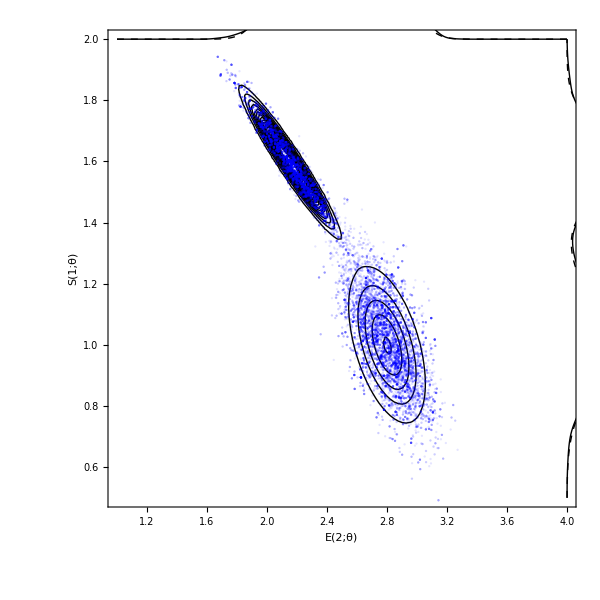

```mathematica
Show[ContourPlot[PDF[MultinormalDistribution[{2.15,1.6},{{0.0184,-0.013},{-0.013, 0.01}}],{x,y}]+PDF[MultinormalDistribution[{2.8,1.0},{{0.02,-0.01},{-0.01,0.02}}],{x,y}],{x,1,4},{y,0.5,2},Frame->True,FrameLabel->{"E(2;θ)","S(1;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,ContourShading->None,PlotRange->Full,Contours->20,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{50,70},{50,120}},Epilog->{{Black,Dashed,Line[Table[{x,2+0.2 PDF[mixdist1,x]},{x,1,4,0.01}]]},{Black,Dashed,Line[Table[{4+0.2 PDF[mixdist2,x],x},{x,0.5,2,0.01}]]},{Black,Line[Table[{x,2+ 0.2 PDF[dist1,x]},{x,1,4,0.01}]]},{Black,Line[Table[{4+0.2 PDF[dist2,x],x},{x,0.5,2,0.01}]]}}],ListPlot[test,PlotStyle->Opacity[0.1,Blue]],ImageSize->600]
```

```mathematica
inputs=Import["../data/mm_bimodal_inputs.csv"];
testi=fSplit[inputs,10000];
testi = Flatten[fPostWarmup[testi],1];
```

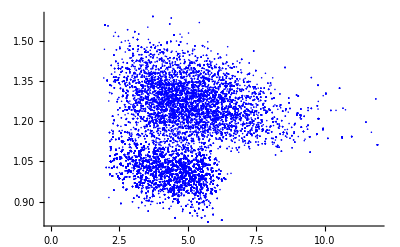

```mathematica
ListPlot[testi[[All,{1,3}]],PlotStyle->Blue]
```

```mathematica
clusters=FindClusters[testi[[All,{1,3}]],3];
```

```mathematica
clustersComp=ClusteringComponents[testi[[All,{1,3}]],3,1];
```

```mathematica
clust1=testi[[Flatten@Position[clustersComp,1],{1,3}]];
clust2=testi[[Flatten@Position[clustersComp,2],{1,3}]];
clust3=testi[[Flatten@Position[clustersComp,3],{1,3}]];
```

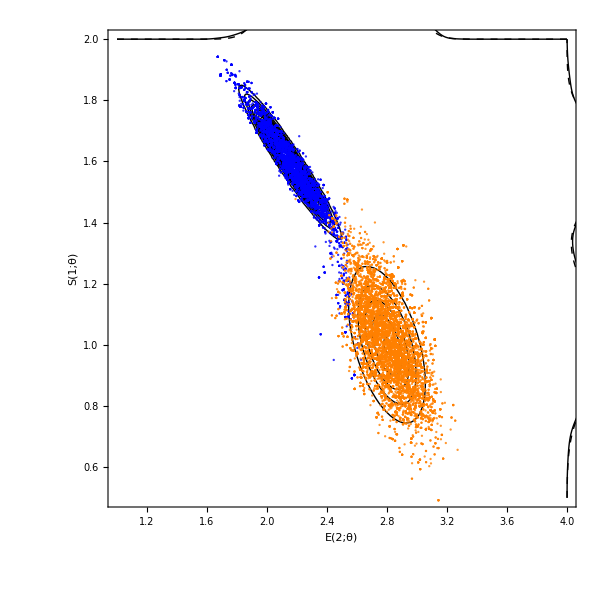

```mathematica
gA=Show[ContourPlot[PDF[MultinormalDistribution[{2.15,1.6},{{0.0184,-0.013},{-0.013, 0.01}}],{x,y}]+PDF[MultinormalDistribution[{2.8,1.0},{{0.02,-0.01},{-0.01,0.02}}],{x,y}],{x,1,4},{y,0.5,2},Frame->True,FrameLabel->{"E(2;θ)","S(1;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,ContourShading->None,PlotRange->Full,Contours->20,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{50,70},{50,120}},Epilog->{{Black,Dashed,Line[Table[{x,2+0.2 PDF[mixdist1,x]},{x,1,4,0.01}]]},{Black,Dashed,Line[Table[{4+0.2 PDF[mixdist2,x],x},{x,0.5,2,0.01}]]},{Black,Line[Table[{x,2+ 0.2 PDF[dist1,x]},{x,1,4,0.01}]]},{Black,Line[Table[{4+0.2 PDF[dist2,x],x},{x,0.5,2,0.01}]]}}],ListPlot[{test[[Flatten@Position[clustersComp,1],All]],test[[Flatten@Position[clustersComp,2],All]],test[[Flatten@Position[clustersComp,3],All]]},PlotStyle->{Opacity[0.8,Blue],Opacity[0.8,Orange],Opacity[0.8,Orange]}],ImageSize->600]
```

```mathematica
Export["../figures/mm_bimodal_outputs.pdf",gA]
```

../figures/mm_bimodal_outputs.pdf

```mathematica
dist1a=SmoothKernelDistribution[testi[[All,1]],0.3];
dist2a=SmoothKernelDistribution[testi[[All,3]],0.03];
```

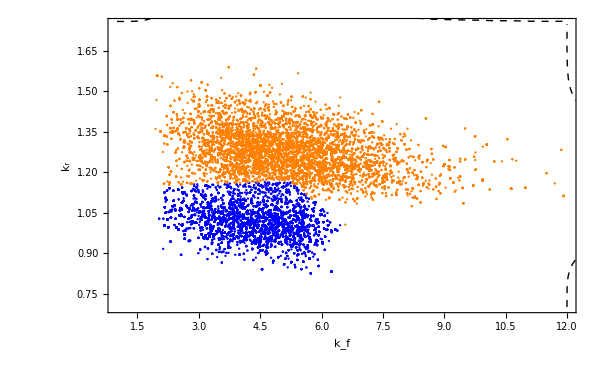

```mathematica
gB=Show[ListPlot[{clust1,clust2,clust3},PlotStyle->{Blue,Orange,Orange},Frame->True,FrameLabel->{"k_f","k_r"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->{{1,12},{0.7,1.75}},PlotRangePadding->0,ImagePadding->{{50,120},{50,70}},PlotRangeClipping->False,Epilog->{{Black,Dashed,Line[Table[{x,1.76+0.8 PDF[dist1a,x]},{x,1,12,0.01}]]},{Black,Dashed,Line[Table[{12+0.8 PDF[dist2a,x],x},{x,0.7,1.75,0.01}]]}}],ImageSize->600]
```

```mathematica
Export["../figures/mm_bimodal_inputs.pdf",gB]
```

../figures/mm_bimodal_inputs.pdf

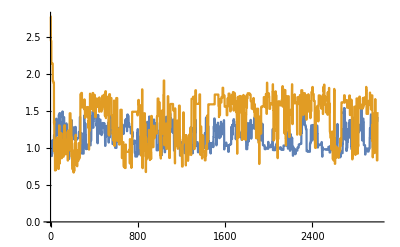

```mathematica
ListLinePlot[{testi[[1;;3000,3]],outputs[[1;;3000,2]]}]
```

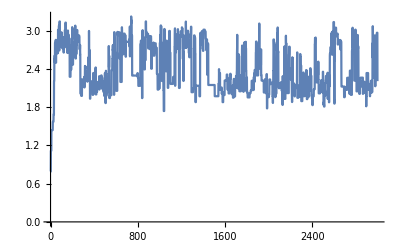

```mathematica
ListLinePlot[outputs[[1;;3000,1]]]
```

## Michaelis Menten 4D

```mathematica
fourDi=Import["../data/mm_4d_inputs.csv"];
```

```mathematica
fourD=Import["../data/mm_4d_outputs.csv"];
```

```mathematica
fourD=fSplit[fourD,10000];
fourD = Flatten[fPostWarmup[fourD],1];
```

```mathematica
aDist=MultinormalDistribution[{0.5,2.8},{{0.015,-0.05},{-0.05,0.3}}];
bDist=MultinormalDistribution[{0.9,1.4},{{0.12,-0.17},{-0.17,0.3}}];
aMarginalDist1=MarginalDistribution[aDist,1];
aMarginalDist2=MarginalDistribution[aDist,2];
bMarginalDist1=MarginalDistribution[bDist,1];
bMarginalDist2=MarginalDistribution[bDist,2];
```

```mathematica
aMarginalDist1a=SmoothKernelDistribution[fourD[[All,1]],0.1];
aMarginalDist2a=SmoothKernelDistribution[fourD[[All,2]],0.4];
bMarginalDist1a=SmoothKernelDistribution[fourD[[All,3]],0.2];
bMarginalDist2a=SmoothKernelDistribution[fourD[[All,4]],0.4];
```

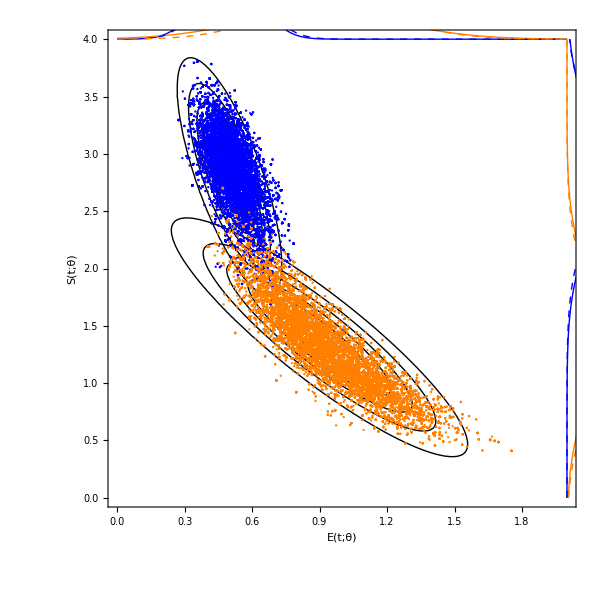

```mathematica
g3=Show[ContourPlot[PDF[aDist,{x,y}],{x,0,2},{y,0,4},Contours->5,ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,Frame->True,FrameLabel->{"E(t;θ)","S(t;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->Full,ImagePadding->{{120,120},{40,120}},Epilog->{{Blue,Line[Table[{x,4+ 0.2 PDF[aMarginalDist1,x]},{x,0,2,0.01}]]},{Orange,Line[Table[{x,4+ 0.2 PDF[bMarginalDist1,x]},{x,0,2,0.01}]]},{Blue,Line[Table[{2+ 0.2 PDF[aMarginalDist2,x],x},{x,0,4,0.01}]]},{Orange,Line[Table[{2+ 0.2 PDF[bMarginalDist2,x],x},{x,0,4,0.01}]]},{Blue,Dashed,Line[Table[{x,4+ 0.2 PDF[aMarginalDist1a,x]},{x,0,2,0.01}]]},{Blue,Dashed,Line[Table[{2+ 0.2 PDF[aMarginalDist2a,x],x},{x,0,4,0.01}]]},{Orange,Dashed,Line[Table[{x,4+ 0.2 PDF[bMarginalDist1a,x]},{x,0,2,0.01}]]},{Orange,Dashed,Line[Table[{2+ 0.2 PDF[bMarginalDist2a,x],x},{x,0,4,0.01}]]}}],ContourPlot[PDF[bDist,{x,y}],{x,0,2},{y,0,4},Contours->5,ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,Frame->True,FrameLabel->{"E(t;θ)","S(t;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->Full],ListPlot[{fourD[[All,1;;2]],fourD[[All,3;;4]]},PlotStyle->{Blue,Orange}],ImageSize->600]
```

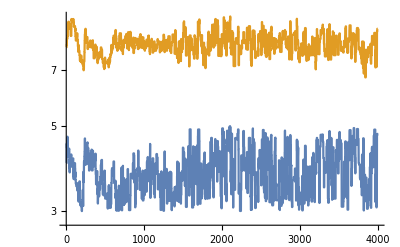

```mathematica
ListLogPlot[Table[fourDi[[1;;4000,i]],{i,4,5,1}],Joined->True]
```

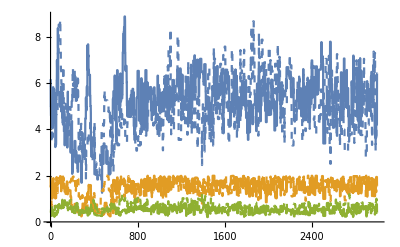

```mathematica
Show[ListLinePlot[Table[fourDi[[10000;;13000,i]],{i,1,3,1}]],ListLinePlot[Table[fourDi[[1;;3000,i]],{i,1,3,1}],PlotStyle->Dashed]]
```

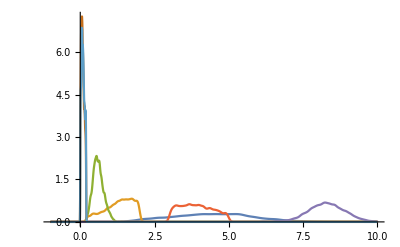

```mathematica
SmoothHistogram[Table[fourDi[[All,i]],{i,1,7,1}],PlotRange->{{-1,10},Full}]
```

```mathematica
contour=Import["../data/mm_4d_contour_vols.csv"];
```

```mathematica
Dimensions@contour
```

{20000,4}

```mathematica
g1=Show[ListPlot[contour[[All,{1,2}]],PlotStyle->Opacity[0.4,Blue],PlotMarkers->{Automatic,5},Frame->{True,True,False,False},FrameLabel->{"E(1;θ)","S(1;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->{{0,5},{0,8}},AspectRatio->1],ContourPlot[PDF[aDist,{x,y}],{x,0,5},{y,0,8},Contours->5,ContourShading->None,Frame->True,FrameLabel->{"E(t;θ)","S(t;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->Full,ContourStyle->Directive[Thick,Black],PlotPoints->100]];
```

```mathematica
g2=Show[ListPlot[contour[[All,{3,4}]],PlotStyle->Opacity[0.4,Blue],PlotMarkers->{Automatic,5},Frame->{True,True,False,False},FrameLabel->{"E(2;θ)","S(2;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->{{0,5},{0,8}},AspectRatio->1],ContourPlot[PDF[bDist,{x,y}],{x,0,5},{y,0,8},Contours->5,ContourShading->None,Frame->True,FrameLabel->{"E(t;θ)","S(t;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,PlotRange->Full,ContourStyle->Directive[Thick,Black],PlotPoints->100]];
```

```mathematica
Export["../figures/mm_4d_contour_vols_1.png",g1,ImageResolution->300]
```

../figures/mm_4d_contour_vols_1.png

```mathematica
Export["../figures/mm_4d_contour_vols_2.png",g2,ImageResolution->300]
```

../figures/mm_4d_contour_vols_2.png

```mathematica
Export["../figures/mm_4d_outputs1.pdf",g3]
```

../figures/mm_4d_outputs.pdf

```mathematica
fourDi=fSplit[fourDi,10000];
fourDi= Flatten[fPostWarmup[fourDi],1];
```

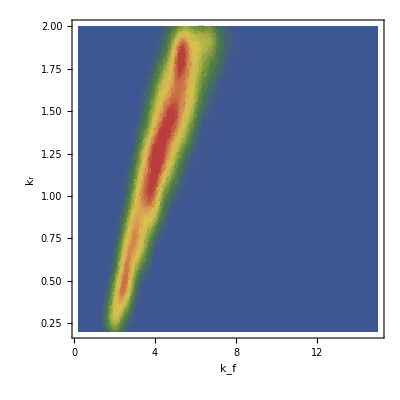

```mathematica
SmoothDensityHistogram[fourDi[[All,{1,2}]],Mesh->10,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.2,15},{0.2,2}},Frame->{True,True,False,False},FrameLabel->{"k_f","k_r"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400]
```

```mathematica
Mean@fourDi
```

{4.37399,1.25758,0.621482,3.92107,8.35647,0.0986106,0.0995876}

```mathematica
Variance@fourDi
```

{1.87886,0.230871,0.0336548,0.2862,0.332004,0.00293814,0.0031384}

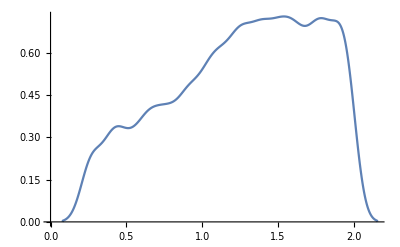

```mathematica
SmoothHistogram[fourDi[[All,2]]]
```

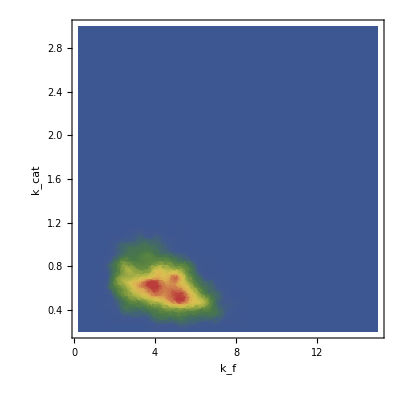

```mathematica
SmoothDensityHistogram[fourDi[[All,{1,3}]],Mesh->10,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.2,15},{0.2,3}},Frame->{True,True,False,False},FrameLabel->{"k_f","k_cat"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400]
```

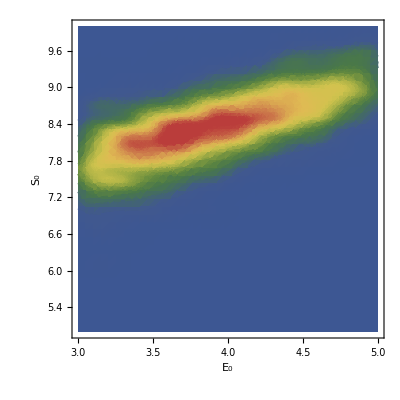

```mathematica
SmoothDensityHistogram[fourDi[[All,{4,5}]],Mesh->10,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{3,5},{5,10}},Frame->{True,True,False,False},FrameLabel->{"E_0","S_0"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400]
```

## TNF

### Bimodal

```mathematica
outputs=Import["../data/tnf_bimodal1_outputs.csv"];
```

```mathematica
Dimensions@outputs
```

{80000,3}

```mathematica
test=fSplit[outputs,20000];
test = Flatten[fPostWarmup[test],1];
```

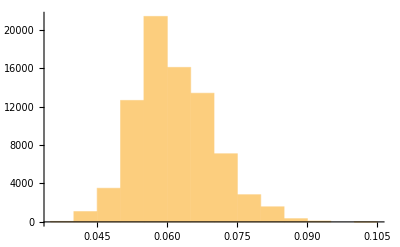

```mathematica
Histogram[outputs[[All,1]]]
```

### Circular

```mathematica
outputs=Import["../data/tnf_bimodal_circular_outputs.csv"];
```

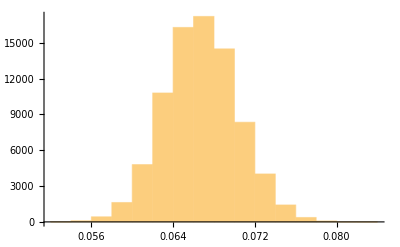

```mathematica
Histogram[outputs[[All,2]]]
```

```mathematica
inputs=Import["../data/tnf_bimodal_circular_inputs.csv"];
```